```mathematica
Clear["Global`*"];
```

```mathematica
ϵ0=8.85418781*^-12;h=6.62607015*^-34;ℏ=h/(2Pi);c=2.99792*^8;km=2Pi/(759*^-9);
m=171*1.660539*^-27;Er=(ℏ*km)^2/(2m);α=179.3au;
au=1.6488*^-41;e=1.602*^-19;
```

```mathematica
Off[ClebschGordan::phy,ClebschGordan::tri,SixJSymbol::tri,SixJSymbol::phy]
```

```mathematica
Er*2*ϵ0*c/α
```

2.40993×10^6

```mathematica
ω3p={0,0,0};ω3p[[2]]=2Pi*c*17992.007*100-2Pi*c*17288.439*100;ω3p[[3]]=2Pi*c*19710.388*100-2Pi*c*17288.439*100;
```

```mathematica
ω3p[[2]]
```

1.32527×10^14

```mathematica
1/(2*Pi*c/496.2263*^-9+ω3p[[3]])*2*Pi*c
```

4.42987×10^-7

```mathematica
λp={1/(25068.222*100),1/(40563.97*100),1/(44017.60*100),1/(17992.007*100),1/(28857.014*100)};
```

```mathematica
λp//N
```

{3.98911×10^-7,2.46524×10^-7,2.27182×10^-7,5.55802×10^-7,3.46536×10^-7}

```mathematica
ωp=2Pi*c/λp;
```

```mathematica
ωp[[1,n]]-ωp[[3,n]]/.n->3
```

Part::pkspec1: The expression n cannot be used as a part specification.

Part::partd: Part specification {4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification {4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦3,3⟧ is longer than depth of object.

{4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦1,3⟧-{4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦3,3⟧

```mathematica
Akil={1/(5.464*^-9),.8/(9.2*^-9),.65/(43*^-9),1/(866.1*^-9),1/(14.6*^-9)};
```

```mathematica
Aki={{0,0,0,0,0},{0,0,0,0,0,0},
{0,0,0,0,0,0}};
```

```mathematica
Jp={1,1,1,1,1};Lp={1,1,1,1,1};Sp={0,0,0,1,0};
```

```mathematica
totbr[nt_]:=(Sqrt[(2*Jp[[nt]]+1)*(2*0+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{0,1,1}])^2*ωp[[0+1,nt]]^3+
(Sqrt[(2*Jp[[nt]]+1)*(2*1+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{1,1,1}])^2*ωp[[1+1,nt]]^3+
(Sqrt[(2*Jp[[nt]]+1)*(2*2+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{2,1,1}])^2*ωp[[2+1,nt]]^3;
```

```mathematica
br[jbr_,nbr_]:=(Sqrt[(2*Jp[[nbr]]+1)*(2*jbr+1)]*SixJSymbol[{Lp[[nbr]],Jp[[nbr]],1},{jbr,1,1}])^2*ωp[[jbr+1,nbr]]^3/totbr[nbr];
```

```mathematica
br[2,3]
```

Part::partd: Part specification {4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦3,3⟧ is longer than depth of object.

Part::partd: Part specification {4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification {4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦2,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(5 ({4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦3,3⟧)^3)/(12 (1/3 ({4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦1,3⟧)^3+1/4 ({4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦2,3⟧)^3+5/12 ({4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦3,3⟧)^3))

```mathematica
For[i=1,i≤6,i++,
(*Aki[[1,i]]=Akil[[i]]*br[0,i];*)
Aki[[1,i]]=Akil[[i]]*br[0,i];
Aki[[2,i]]=Akil[[i]]*br[1,i];
Aki[[3,i]]=Akil[[i]]*br[2,i];
]
```

Part::partd: Part specification {4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification {4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 6 of {1.83016×10^8,8.69565×10^7,1.51163×10^7,1.1546×10^6,6.84932×10^7} does not exist.

Part::partw: Part 6 of {1,1,1,1,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::partw: Part 6 of {(6.10054×10^7 ({4.72197×10^15,«3»,5.43565×10^15}⟦1,1⟧)^3)/(1/3 ({«5»}⟦1,1⟧)^3+1/4 ({«5»}⟦2,1⟧)^3+5/12 ({«5»}⟦3,1⟧)^3),(2.89855×10^7 («1»)^3)/(1/3 ({«5»}⟦1,2⟧)^3+1/4 («1»)^3+5/12 («1»)^3),(«1»)/(«1»),(«19» («1»)^3)/(1/3 («1»)^3+«1»+«1»),(2.28311×10^7 («1»⟦1,5⟧)^3)/(1/3 ({«5»}⟦1,5⟧)^3+1/4 ({«5»}⟦2,5⟧)^3+5/12 ({«5»}⟦3,5⟧)^3)} does not exist.

```mathematica
RedMatL[na_,j3p_]:=Sqrt[(2*Lp[[na]]+1)*3*ϵ0*h*c^3/2/(ωp[[na]]^3)*Akil[[na]]];
```

```mathematica
RedMat[na_,j3p_]:=(*(((-1)^(Lp[[na]]+1+j3p+1))^1*Sqrt[(2*Jp[[na]]+1)*(2*j3p+1)]*SixJSymbol[{Lp[[na]],Jp[[na]],1},{j3p,1,1}]^1)^(0)*(*Sqrt[j3p+1]factor added to match results for 3P1*)Sqrt[3*ϵ0*h*c^3/(2*ωp[[j3p+1,na]]^3)*(2*Jp[[na]]+1)*Akil[[na]]*ωp[[j3p+1,na]]^3/ωp[[2,na]]^3*(2*Lp[[na]]+1)*(2*j3p+1)*SixJSymbol[{Jp[[na]],1,j3p},{1,1,Lp[[na]]}]^2];*)(-1)^(Lp[[na]]+Sp[[na]]+j3p+1)*Sqrt[(2*Jp[[na]]+1)*(2*j3p+1)]*SixJSymbol[{Jp[[na]],1,j3p},{0,0,Lp[[na]]}]*RedMatL[na,j3p];
```

```mathematica
Clear[Γ3P0,Int];c=2.99792*^8;ϵ0=8.85*^-12;h=6.626*^-34;ℏ=h/(2Pi);
RedMatFfk[fpb_,jpb_,lpb_,fb_,jb_,lb_,nb_]:=(-1)^(jpb+1/2+fb+1)*Sqrt[(2*fpb+1)*(2*fb+1)]*SixJSymbol[{jpb,fpb,1/2},{fb,jb,1}]*RedMat[nb,jpb];
RedMatFki[fpb_,jpb_,lpb_,npb_,fb_,jb_,lb_]:=(-1)^(jpb+1/2+fb+1)*Sqrt[(2*fpb+1)*(2*fb+1)]*SixJSymbol[{jpb,fpb,1/2},{fb,jb,1}]*RedMat[npb,jb];
MEfk[fpa_,mfpa_,jpa_,lpa_,qy_,fa_,mfa_,ja_,la_,na_]:=(-1)^(fpa-mfpa)*ThreeJSymbol[{fpa,-mfpa},{1,qy},{fa,mfa}]*RedMatFfk[fpa,jpa,lpa,fa,ja,la,na];
MEki[fpa_,mfpa_,jpa_,lpa_,npa_,qy_,fa_,mfa_,ja_,la_]:=(-1)^(fpa-mfpa)*ThreeJSymbol[{fpa,-mfpa},{1,qy},{fa,mfa}]*RedMatFki[fpa,jpa,lpa,npa,fa,ja,la];
Da[ω_,qx_,ffin_,mffin_,jfin_,lfin_,qpol_,finit_,mfinit_,jinit_,linit_]:=Sum[Sum[Sum[MEfk[ffin,mffin,jfin,lfin,qx,fk,mfk,Jp[[nk]],Lp[[nk]],nk]*MEki[fk,mfk,Jp[[nk]],Lp[[nk]],nk,qpol,finit,mfinit,jinit,linit]/(ωp[[nk]]+If[nk==4,If[fk==1/2,-1177.231*^6*2Pi,4759.440*^6*2Pi],0]-ω)+MEfk[ffin,mffin,jfin,lfin,qpol,fk,mfk,Jp[[nk]],Lp[[nk]],nk]*MEki[fk,mfk,Jp[[nk]],Lp[[nk]],nk,qx,finit,mfinit,jinit,linit]/(ωp[[nk]]+(ω)),
{mfk,-fk,fk,1}],
{fk,1/2,3/2,1}],
{nk,4,4,1}];
Γ1S0[ω_,Int_,ffin_,mffin_,jfin_,lfin_,qpol_]:=Int*(ω)^3/((4Pi*ϵ0)^2*c^4*ℏ^3)*8Pi/3*Sum[Da[ω,q,ffin,mffin,jfin,lfin,qpol,1/2,1/2,0,0]^2,{q,-1,1,1}];
```

```mathematica
qs=1;fgrn=3/2;mfg=-1/2;MEfk[1/2,mfg,0,1,-qs,fgrn,mfg+qs,1,1,4]*MEki[fgrn,mfg+qs,1,1,4,qs,1/2,mfg,0,1]
```

2.34325×10^-60

```mathematica
MEfk[1/2,-1/2,0,1,0,1/2,-1/2,1,1,4]*MEki[1/2,-1/2,1,1,4,0,1/2,-1/2,0,1]
```

-2.34325×10^-60

```mathematica
Γel[Δ_,θ_,Int_]:=(1/2)*Int*(ωp[[4]]+4759.440*^6*2Pi+Δ)^3/((4Pi*ϵ0)^2*c^4*ℏ^3)*8Pi/3*(1/2*Sum[(Da[ωp[[4]]+4759.440*^6*2Pi+Δ,q,1/2,1/2,0,0,0,1/2,1/2,0,0]-Da[ωp[[4]]+4759.440*^6*2Pi+Δ,q,1/2,-1/2,0,0,0,1/2,-1/2,0,0]),{q,-1,1,1}]^2+1/4*Sum[(Da[ωp[[4]]+4759.440*^6*2Pi+Δ,q,1/2,1/2,0,0,1,1/2,1/2,0,0]-Da[ωp[[4]]+4759.440*^6*2Pi+Δ,q,1/2,-1/2,0,0,1,1/2,-1/2,0,0]),{q,-1,1,1}]^2+1/4*Sum[(Da[ωp[[4]]+4759.440*^6*2Pi+Δ,q,1/2,1/2,0,0,-1,1/2,1/2,0,0]-Da[ωp[[4]]+4759.440*^6*2Pi+Δ,q,1/2,-1/2,0,0,-1,1/2,-1/2,0,0]),{q,-1,1,1}]^2)
```

```mathematica
Γel[-3727.278*^6*2Pi,Pi/2,526*^4]
```

1058.22

```mathematica
ramanScatt[Δ_,mFfin_,θ_,Int_]:=Γ1S0[ωp[[4]]+4759.440*^6*2Pi+Δ,Int*1/2,1/2,mFfin,0,0,0]+Γ1S0[ωp[[4]]+4759.440*^6*2Pi+Δ,Int*1/4,1/2,mFfin,0,0,1]+Γ1S0[ωp[[4]]+4759.440*^6*2Pi+Δ,Int*1/4,1/2,mFfin,0,0,-1];
(*Scattering from x beam... Δ=184 MHz usually*)
```

```mathematica
(Γel[Δ*2Pi,Pi/2,526*^4]+ramanScatt[Δ*2Pi,-1/2,Pi/2,526*^4])/Abs[(5.2*^6)*((1/Δ-1/(5936.67*^6+Δ))/(1/-3727.278*^6-1/(5936.67*^6-3727.278*^6)))]/4/.Δ->-3727.278*^6
```

0.00012719

```mathematica
(ΓelZ[Δ*2Pi,382*^4]+ramanScattZ[Δ*2Pi,-1/2,382*^4])/Abs[(3.5*^6)*((1/Δ-1/(5936.67*^6+Δ))/(1/-3707.278*^6-1/(5936.67*^6-3707.278*^6)))]/4/.Δ->-3727*^6
```

7.11733×10^-8 (ramanScattZ[-7454000000 π,-1/2,3820000]+ΓelZ[-7454000000 π,3820000])

```mathematica
Abs[(5.2*^6)*((1/Δ-1/(5936.67*^6+Δ))/(1/-3727.278*^6-1/(5936.67*^6-3727.278*^6)))]/.Δ->6800*^6
```

494428.

```mathematica
ramanScattZ[Δ_,mFfin_,Int_]:=(Γ1S0[ωp[[4]]+4759.440*^6*2Pi+Δ,Int,1/2,mFfin,0,0,-1]+Γ1S0[ωp[[4]]+4759.440*^6*2Pi+Δ,Int,1/2,mFfin,0,0,1])/2;
(*Scattering from Z beam... sigma+ polarized*)
```

```mathematica
ΓelZ[Δ_,Int_]:=(1/2)*Int*(ωp[[4]]+4759.440*^6*2Pi+Δ)^3/((4Pi*ϵ0)^2*c^4*ℏ^3)*8Pi/3*Sum[(Da[ωp[[4]]+4759.440*^6*2Pi+Δ,q,1/2,1/2,0,0,-1,1/2,1/2,0,0]-Da[ωp[[4]]+4759.440*^6*2Pi+Δ,q,1/2,-1/2,0,0,-1,1/2,-1/2,0,0]),{q,-1,1,1}]^2
```

```mathematica
ramanScattZ[-3707.278*^6*2Pi,-1/2,235*^4]
```

469.359

```mathematica
ΓelZ[-3707.278*^6*2Pi,235*^4]
```

938.719

```mathematica
1410/3*^6/4.
```

0.0001175

```mathematica
Γel[-3727.278*^6*2Pi,0,346*^4]
```

696.094

```mathematica
ramanScatt[-3727.278*^6*2Pi,-1/2,0,346*^4]
```

1044.14

```mathematica
Δtest=-12000*^6;
Ω=Abs[(4.465*^6)*((1/Δtest-1/(5936.67*^6+Δtest))/(1/-3727.278*^6-1/(5936.67*^6-3727.278*^6)))];
(Γel[Δtest*2Pi,0,Int]+ramanScatt[Δtest*2Pi,-1/2,0,Int])/Ω/4/.Int->346*^4
```

0.0000110275

```mathematica
Δtest=-11980*^6;
Ω=Abs[(3*^6)*((1/Δtest-1/(5936.67*^6+Δtest))/(1/-3707.278*^6-1/(5936.67*^6-3707.278*^6)))];
(ΓelZ[Δtest*2Pi,Int]+ramanScattZ[Δtest*2Pi,-1/2,Int])/Ω/4/.Int->235*^4
```

0.0000133947

```mathematica
ramanScatt[-3707.278*^6*2Pi,-1/2,0,382*^4]
```

1144.44

```mathematica
ramanScattZ[-3707.278*^6*2Pi,-1/2,382*^4]
```

762.959

```mathematica
3020/3.5*^6/4
```

0.000215714

```mathematica
2620/5.2*^6/4
```

0.000125962

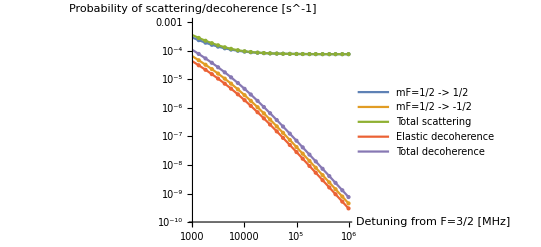

```mathematica
Clear[Δ];ϕ=45(*50.768479514174686*);LogLogPlot[{(*ramanScatt[Δ*1*^6*2Pi,1/2,26.5652/360*2Pi,201113*Δ/-184],ramanScatt[Δ*1*^6*2Pi,-1/2,26.5652/360*2Pi,201113*Δ/-184],*)1/1.47*^6/4*Abs[ramanScatt[Δ*1*^6*2Pi,1/2,ϕ/360*2Pi,132011*Δ*(5936.67+Δ)/(-177)/(5936.67-177)]],1/1.47*^6/4*Abs[ramanScatt[Δ*1*^6*2Pi,-1/2,ϕ/360*2Pi,132011*(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]],1/1.47*^6/4*Abs[ramanScatt[Δ*1*^6*2Pi,1/2,ϕ/360*2Pi,132011*Δ*(5936.67+Δ)/(-177)/(5936.67-177)]+ramanScatt[Δ*1*^6*2Pi,-1/2,ϕ/360*2Pi,132011*Δ*(5936.67+Δ)/(-177)/(5936.67-177)]],1/1.47*^6/4*Abs[Γel[Δ*1*^6*2Pi,ϕ/360*2Pi,132011*(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]],1/1.47*^6/4*Abs[ramanScatt[Δ*1*^6*2Pi,-1/2,ϕ/360*2Pi,132011*(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]+Γel[Δ*1*^6*2Pi,ϕ/360*2Pi,132011*(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]]},{Δ,1000,1*^6},PlotLegends->{"mF=1/2 -> 1/2","mF=1/2 -> -1/2","Total scattering","Elastic decoherence","Total decoherence"},AxesLabel->{"Detuning from F=3/2 [MHz]","Probability of scattering/decoherence [s^-1]"},PlotRange->{1*^-10,.001},PlotPoints->25,Mesh->All,MaxRecursion->0]
```

```mathematica
ϕ=45;Abs[ramanScatt[Δ*1*^6*2Pi,-1/2,ϕ/360*2Pi,132011*(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]+Γel[Δ*1*^6*2Pi,ϕ/360*2Pi,132011*(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]]/.Δ->-3805
```

539.663

```mathematica
539.7*1/1.47*^6/2
```

0.000183571

```mathematica
Abs[ramanScatt[Δ*1*^6*2Pi,-1/2,ϕ/360*2Pi,132011*(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]+Γel[Δ*1*^6*2Pi,ϕ/360*2Pi,132011*(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]]/.Δ->6800
```

50.5427

```mathematica
50.5*1/1.47*^6/2
```

0.0000171769

```mathematica
FindMinimum[ramanScatt[Δ*1*^6*2Pi,-1/2,ϕ/360*2Pi,132011*(16.1^2/177)/(16.1^2/(-Δ)+11.4*22.8/((5936.67+Δ)))]+Γel[Δ*1*^6*2Pi,ϕ/360*2Pi,132011*(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))],{Δ,-5936.67/2}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{544.145,{Δ→-2969.24}}

```mathematica
FindMinimum[Abs[ramanScatt[Δ*1*^6*2Pi,1/2,ϕ/360*2Pi,186700*Δ*(5936.67+Δ)/(-177)/(5936.67-177)]+ramanScatt[Δ*1*^6*2Pi,-1/2,ϕ/360*2Pi,186700*Δ*(5936.67+Δ)/(-177)/(5936.67-177)]],{Δ,-5936.67/2}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{596.174,{Δ→-3477.64}}

```mathematica
467.018/(1.47*^6)/4
```

0.0000794248

```mathematica
Rationalize[0.00010136054421768709]
```

149/1470000

```mathematica
ϕ=90-61.78;Abs[ramanScatt[Δ*1*^6*2Pi,-1/2,ϕ/360*2Pi,156040*(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]+Γel[Δ*1*^6*2Pi,ϕ/360*2Pi,156040*(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]]/.Δ->-177
```

5636.43

```mathematica
Abs[ramanScatt[Δ*1*^6*2Pi,-1/2,ϕ/360*2Pi,155]+Γel[Δ*1*^6*2Pi,ϕ/360*2Pi,155]]/.Δ->-77
```

22.8922

```mathematica
5636.43*680*^-9/4
```

0.000958193

```mathematica
1.9*.01
```

0.019

```mathematica
17/1.47*^6/4
```

2.89116×10^-6

```mathematica
ramanScatt[Δ*1*^6*2Pi,1/2,26.5652/360*2Pi,161072*(16.1^2/177)/(16.1^2/(-Δ)+11.4*22.8/((5936.67+Δ)))]+ramanScatt[Δ*1*^6*2Pi,-1/2,26.5652/360*2Pi,161072*(16.1^2/177)/(16.1^2/(-Δ)+11.4*22.8/((5936.67+Δ)))]/.Δ->-3500
```

498.259

```mathematica
Plot[{ramanScatt[Δ*1*^6*2Pi,1/2,26.5652/360*2Pi],ramanScatt[Δ*1*^6*2Pi,-1/2,26.5652/360*2Pi],ramanScatt[Δ*1*^6*2Pi,1/2,26.5652/360*2Pi]+ramanScatt[Δ*1*^6*2Pi,-1/2,26.5652/360*2Pi]},{Δ,-6000,0},PlotLegends->{"mF=1/2 -> 1/2","mF=1/2 -> -1/2","Total"},AxesLabel->{"Detuning from F=3/2 [MHz]","Scattering rate [s^-1]"}]
```

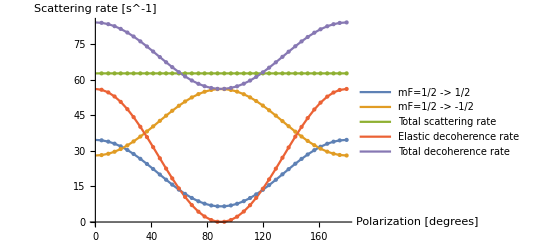

```mathematica
Plot[{ramanScatt[-3000*1*^6*2Pi,1/2,θ/360*2Pi,161072],ramanScatt[-3000*1*^6*2Pi,-1/2,θ/360*2Pi,161072],ramanScatt[-3000*1*^6*2Pi,1/2,θ/360*2Pi,161072]+ramanScatt[-3000*1*^6*2Pi,-1/2,θ/360*2Pi,161072],Γel[-3000*1*^6*2Pi,θ/360*2Pi,161072],ramanScatt[-3000*1*^6*2Pi,-1/2,θ/360*2Pi,161072]+Γel[-3000*1*^6*2Pi,θ/360*2Pi,161072](*ramanScatt[-177*1*^6*2Pi,1/2,θ/360*2Pi,161072]+ramanScatt[-177*1*^6*2Pi,-1/2,θ/360*2Pi,161072]*)},{θ,0,180},AxesLabel->{"Polarization [degrees]","Scattering rate [s^-1]"},PlotPoints->40,Mesh->All,MaxRecursion->0,PlotLegends->{"mF=1/2 -> 1/2","mF=1/2 -> -1/2","Total scattering rate","Elastic decoherence rate","Total decoherence rate"}]
```

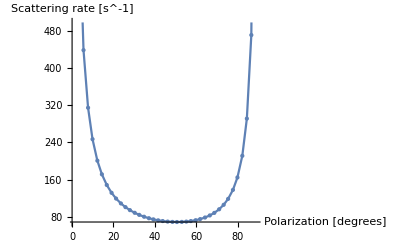

```mathematica
Plot[{(ramanScatt[-3000*1*^6*2Pi,-1/2,θ/360*2Pi,161072]+Γel[-3000*1*^6*2Pi,θ/360*2Pi,161072])/Sin[2θ/360*2Pi](*ramanScatt[-177*1*^6*2Pi,1/2,θ/360*2Pi,161072]+ramanScatt[-177*1*^6*2Pi,-1/2,θ/360*2Pi,161072]*)},{θ,1,89},AxesLabel->{"Polarization [degrees]","Scattering rate [s^-1]"},PlotPoints->40,Mesh->All,MaxRecursion->0(*,PlotLegends->{"mF=1/2 -> 1/2","mF=1/2 -> -1/2","Elastic decoherence rate","Total decoherence rate"}*)]
```

```mathematica
FindMinimum[(ramanScatt[-3000*1*^6*2Pi,-1/2,θ/360*2Pi,161072]+Γel[-3000*1*^6*2Pi,θ/360*2Pi,161072])/Sin[2θ/360*2Pi],{θ,45}]
```

{68.7327,{θ→50.7685}}

```mathematica
ramanScatt[Δ*1*^6*2Pi,1/2]+ramanScatt[Δ*1*^6*2Pi,-1/2]/.Δ->-177
```

14784.

```mathematica
Γ1S0[ωp[[4]]-164*^6*(2Pi),58100,1/2,var,0,0,-1]/.var->1/2
```

$Assumptions::cas: Warning: contradictory assumption(s) -5/2-var==0&&-1/2≤-var≤1/2&&-2 var∈&&1/2+var∈&&-1/2≤var≤1/2 encountered.

$Assumptions::cas: Warning: contradictory assumption(s) -3/2-var==0&&-1/2≤-var≤1/2&&-2 var∈&&1/2+var∈&&-1/2≤var≤1/2 encountered.

General::stop: Further output of $Assumptions::cas will be suppressed during this calculation.

828.741

```mathematica
ωp[4]-184*^6*(2Pi)
```

-368000000 π+{4.72197×10^15,7.64083×10^15,8.29137×10^15,3.38906×10^15,5.43565×10^15}[4]

```mathematica
Plot[Γ1S0[2Pi*c/λ,2.39*^6,1/2,-1/2,0,0]*10^4,{λ,500*^-9,1000*^-9},PlotRange->{0,10}]
```

$Aborted

```mathematica
Γ1S0ΔmF[ω_]=Γ1S0[ω,10*^6,1/2,-1/2,0,0]*10^4;
```

```mathematica
Plot[Γ1S0ΔmF[2Pi*c/λ*1*^9],{λ,554,558},PlotRange->{0,40},AxesLabel->{"Wavelength [nm]","Scattering rate [10^-4 s^-1/(kW/cm^2)"}]
```

-Graphics-

```mathematica
Γ3P03P1[ω_]=Sum[Sum[Γ3P0[ω,2.39*^6,f,mf,1,1]*10^4,{mf,-1/2,f,1}],{f,1/2,3/2,1}];
```

```mathematica
Γ3P03P1[2Pi*c/(759*^-9)]
```

10000 Γ3P0[2.48175×10^15,2.39×10^6,1/2,-1/2,1,1]+10000 Γ3P0[2.48175×10^15,2.39×10^6,1/2,1/2,1,1]+10000 Γ3P0[2.48175×10^15,2.39×10^6,3/2,-1/2,1,1]+10000 Γ3P0[2.48175×10^15,2.39×10^6,3/2,1/2,1,1]+10000 Γ3P0[2.48175×10^15,2.39×10^6,3/2,3/2,1,1]

```mathematica
Plot[Γ3P03P1[2Pi*c/λ],{λ,300*^-9,1.5*^-6},PlotRange->{0,10}]
```

-Graphics-

```mathematica
Da[km*c,0,1/2,1/2,0,1]
```

Da[2.48175×10^15,0,1/2,1/2,0,1]

```mathematica
ℏ*α
```

3.1176×10^-73

```mathematica
Γ3P03P2[ω_]=Sum[Sum[Γ3P0[ω,2.39*^6,f,mf,2,1]*10^4,{mf,-1/2,f,1}],{f,1/2,5/2,1}];
```

```mathematica
Plot[Γ3P03P2[2Pi*c/λ],{λ,300*^-9,1.5*^-6},PlotRange->{0,10}]
```

-Graphics-

```mathematica
ΩR=Sqrt[1.47*^6*177*^6]
```

1.61304×10^7

```mathematica
ΩR=16.1*^6;
Γ=183.02086*^3;
λ=555.6481*^-9;
ϵ0=8.85418781*^-12;
h=6.62607015*^-34;
c=2.99792458*^8;
μ=Sqrt[3*ϵ0*h*λ^3/(2*(2Pi)^2)*3*Γ];
```

```mathematica
μ
```

4.58225×10^-30

```mathematica
1/874.*^-9/(2Pi)
```

182099.

```mathematica
pi32factor=ThreeJSymbol[{3/2,-1/2},{1,0},{1/2,1/2}]*Sqrt[2*4]*SixJSymbol[{1,3/2,1/2},{1/2,0,1}]
```

(√2)/3

```mathematica
1/2*c*ϵ0*(ΩR*h/(μ*pi32factor))^2(*pi polarization*)
```

50.8937

```mathematica
sigma32factor=ThreeJSymbol[{3/2,-1/2},{1,1},{1/2,-1/2}]*Sqrt[2*4]*SixJSymbol[{1,3/2,1/2},{1/2,0,1}]
```

1/3

```mathematica
1/2*c*ϵ0*(ΩR*h/(μ*sigma32factor))^2(*sigma polarization*)
```

101.787

```mathematica
32214+2*64428
```

161070

```mathematica
pi12factor=-ThreeJSymbol[{1/2,-1/2},{1,0},{1/2,1/2}]*Sqrt[2*2]*SixJSymbol[{1,1/2,1/2},{1/2,0,1}]
```

-1/3

```mathematica
Ωpi12=-Sqrt[32214.5/(1/2*c*ϵ0)]*μ*pi12factor/h
```

2.86421×10^8

```mathematica
sigma12factor=-ThreeJSymbol[{1/2,-1/2},{1,1},{1/2,-1/2}]*Sqrt[2*2]*SixJSymbol[{1,1/2,1/2},{1/2,0,1}]
```

(√2)/3

```mathematica
Ωsigma12=Sqrt[64428.9/(1/2*c*ϵ0)]*μ*sigma12factor/h
```

2.27229×10^7

```mathematica
1/(2*1.47*^6*1/Sin[2*26.56/360*2Pi])*498.259
```

0.000135563

```mathematica
1/Sin[26.56/360*2Pi]
```

2.23646

```mathematica
Sqrt[11.4*22.8]
```

16.122

```mathematica
NSolve[{Ωπ*Ωσ==177*^6*1/(680*^-9),Iπ==1/2*c*ϵ0(h*Ωπ/(μ*1/3))^2,Iσ==1/2*c*ϵ0(h*Ωσ/(μ*Sqrt[2]/3))^2,Iπ==I0*Sin[(90-61.78)/360*2Pi]^2,Iσ==I0*Cos[(90-61.78)/360*2Pi]^2/2},{Iπ,Iσ,Ωπ,Ωσ,I0}]
```

{{Iπ→-34888.9,Iσ→-60573.7,Ωπ→0.-1.18189×10^7 ⅈ,Ωσ→0.+2.20236×10^7 ⅈ,I0→-156036.},{Iπ→-34888.9,Iσ→-60573.7,Ωπ→0.+1.18189×10^7 ⅈ,Ωσ→0.-2.20236×10^7 ⅈ,I0→-156036.},{Iπ→34888.9,Iσ→60573.7,Ωπ→1.18189×10^7,Ωσ→2.20236×10^7,I0→156036.},{Iπ→34888.9,Iσ→60573.7,Ωπ→-1.18189×10^7,Ωσ→-2.20236×10^7,I0→156036.}}

```mathematica
2.20236*^7*h/(μ*Sqrt[2]/3)
```

6755.72

```mathematica
1.18189*^7*h/(μ*1/3)
```

5127.14

```mathematica
6738/5113.
```

1.31782

```mathematica
155217*Sin[61.78/360*2Pi]*Cos[61.78/360*2Pi]/(Sin[50.7685/360*2Pi]*Cos[50.7685/360*2Pi])
```

132011.

```mathematica
1.47*^6*177*^6/(μ^2/3^2*2/(c*ϵ0)/h^2*Sin[61.78/360*2Pi]*Cos[61.78/360*2Pi]/2*Sqrt[2])/Sin[2*50.7685/360*2Pi]*Sin[2*61.78/360*2Pi]
```

186692.

```mathematica
Abs[(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]/.Δ->40000
```

1802.39

```mathematica
Abs[(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]5.3/.5/.Δ->-3805
```

84.3353

```mathematica
Abs[(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]/.Δ->-5936.67-6770
```

84.3819

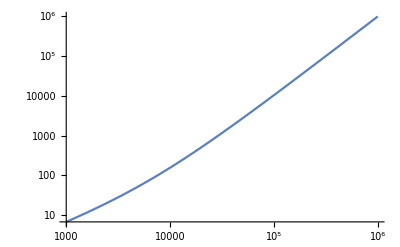

```mathematica
LogLogPlot[Abs[(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))],{Δ,1000,1000000}]
```

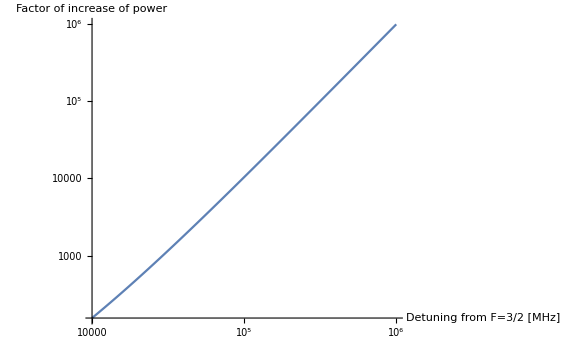

```mathematica
LogLogPlot[Abs[(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))],{Δ,10000,1000000},AxesLabel->{"Detuning from F=3/2 [MHz]","Factor of increase of power"}]
```

```mathematica
Abs[(1/177+1/(5936.67-177))/(1/(-Δ)+1/((5936.67+Δ)))]/.Δ->13000
```

241.477

```mathematica
1/.002/.1
```

5000.

```mathematica
3180/13.2
```

240.909

```mathematica
90*^-9/15.*^-3
```

6.×10^-6

```mathematica
Sqrt[4*164*^6/(1.4*^-6)]
```

2.16465×10^7

```mathematica
1/2*c*ϵ0*(h*2.165*^7/(μ*Sqrt[2]/3))^2
```

58506.9